## Linear stability analysis of two-species interaction

### → Species only differ in soil and resource preference; Intrinsic growth rate is quadratic

```mathematica
ClearAll["α"]
```

#### Eq(1) from the paper. Using S instead of E since mathematica does not allow that.

```mathematica
Subscript[dN, 1]=Subscript[N, 1](1-S^2/ω^2-(Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]=Subscript[N, 2](1-(S-ϵ)^2/ω^2-(α Subscript[N, 1]+Subscript[N, 2]));
dS=(-S)Subscript[N, 1]+(ϵ-S)Subscript[N, 2];
```

#### Equilibrium

```mathematica
eqN=FullSimplify[Solve[Subscript[dN, 1]==0&&Subscript[dN, 2]==0,{Subscript[N, 1],Subscript[N, 2]}]]
```

{{N_1→0,N_2→0},{N_1→0,N_2→1-(S-ϵ)^2/ω^2},{N_1→(-S^2 (-1+α)+2 S α ϵ-α ϵ^2+(-1+α) ω^2)/((-1+α^2) ω^2),N_2→(-S^2 (-1+α)-2 S ϵ+ϵ^2+(-1+α) ω^2)/((-1+α^2) ω^2)},{N_1→1-S^2/ω^2,N_2→0}}

→ Four equilibrium. (1) Both extinct, (2) Only species 1 persists, (3) Coexistence, (4) Only species 2 persists

```mathematica
FullSimplify[Reduce[(Subscript[N, 1]/.eqN[[3]])>0&&0<α<1&&ω>0,S,PositiveReals]]
```

ω>0&&ϵ>0&&0<α<1&&0<S<(α ϵ)/(-1+α)+√((α ϵ^2)/(-1+α)^2+ω^2)

```mathematica
Reduce[(α ϵ)/(-1+α)+√((α ϵ^2)/(-1+α)^2+ω^2)>0&&0<α<1&&ω>0,α]
```

ϵ∈ℝ&&ω>0&&0<α<1

→ All four roots (multiple coexistence equilibria) are feasible for some values of S

```mathematica
eqS1=FullSimplify[Solve[(dS/.eqN[[3]])==0,S]]
```

{{S→ϵ/2},{S→ϵ/2-(√((3+α) ϵ^2+4 (-1+α) ω^2))/(2 √(-1+α))},{S→ϵ/2+(√((3+α) ϵ^2+4 (-1+α) ω^2))/(2 √(-1+α))}}

→ All three roots are real when ϵ^2 < 4 ω^2 (1-α)/(3+α)  [C1]. C1 is red line in the figure below.

#### Stability

```mathematica
Jc={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}}
```

{{1-S^2/ω^2-2 N_1-α N_2,-α N_1,-(2 S N_1)/ω^2},{-α N_2,1-(S-ϵ)^2/ω^2-α N_1-2 N_2,-(2 (S-ϵ) N_2)/ω^2},{-S,-S+ϵ,-N_1-N_2}}

```mathematica
FullSimplify[Eigensystem[Jc/.eqN[[1]]]]
```

{{0,1-S^2/ω^2,1-(S-ϵ)^2/ω^2},{{0,0,1},{-1/S+S/ω^2,0,1},{0,1/(-S+ϵ)+(S-ϵ)/ω^2,1}}}

→ Extinction is never stable. It is stable on the N_1 x N_2 plane when S is not within the fundamental niche of either species.

```mathematica
FullSimplify[Eigenvalues[Jc/.eqN[[2]]/.S-> ϵ]]
```

{-1,-1,1-α-ϵ^2/ω^2}

→ Competitive exclusion is stable when ϵ^2 > ω^2(1-α) [C2]. Blue line in figure below

```mathematica
FullSimplify[Eigenvalues[Jc/.eqN[[3]]/.eqS1[[1]]]]
```

{-1+ϵ^2/(4 ω^2),-((-3+α) ϵ^2-4 (-3+α) ω^2+√(1+α) √(ϵ^2-4 ω^2) √((-15+α) ϵ^2-4 (1+α) ω^2))/(8 (1+α) ω^2),(-((-3+α) ϵ^2)+4 (-3+α) ω^2+√(1+α) √(ϵ^2-4 ω^2) √((-15+α) ϵ^2-4 (1+α) ω^2))/(8 (1+α) ω^2)}

```mathematica
FullSimplify[Reduce[(-15+α) ϵ^4-8 (-7+α) ϵ^2 ω^2+16 (1+α) ω^4>0&&ω>0&&0<α<1,ϵ]]
```

0<α<1&&-2 ω<ϵ<2 ω

```mathematica
FullSimplify[Reduce[(-3+α) ϵ^2-4 (-3+α) ω^2+√(1+α) √((-15+α) ϵ^4-8 (-7+α) ϵ^2 ω^2+16 (1+α) ω^4)>0&&ω>0&&0<α<1,ϵ]]
```

0<α<1&&-2 ω<ϵ<2 ω

→  Symmetric coexistence equilibrium is stable whenever -2ω < ϵ < 2ω and [C2] does not hold

```mathematica
Manipulate[Plot[{0,S/.eqS1[[1]],ϵ,S/.eqS1[[2]]/.ω->w/.α->a,S/.eqS1[[3]]/.ω->w/.α->a},{ϵ,0,2.5},PlotStyle->Black,GridLines->{{{(w√(1-a)),Blue},{(2w√((1-a)/(3+a))),Red},{2w,Gray}},{}},Frame-> True,FrameLabel->{ϵ,SuperStar[S]}],{{a,0,α},0,0.99},{{w,1,ω},0.1,2}]
```

→ Blue line separates regions of stable coexistence. Coexistence and competitive exclusion are alternative stables states between the red and blue lines.
    Asymmetric coexistence (the curves) are either unstable (after the blue line; not analytic but see the figure above and numerics below) or unfeasible (before the blue line) .

#### Competition coefficient (α) calculation

```mathematica
ClearAll["αc","f"]
```

```mathematica
f[ν_,σ_,ζ_]:=ν NIntegrate[Exp[-x^2/σ^2]Exp[(-(x-ζ)^4)/(81 σ^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[-x^2/σ^2]^2,{x,-Infinity,Infinity}]
```

#### Figure 2a equivalent for quadratic intrinsic growth rate

```mathematica
par={ω->1,σ->1,ν->1};
```

```mathematica
3^(1/2)
```

√3

```mathematica
αc=f[ν,σ,ζ]/.par;
```

NIntegrate::inumr: The integrand ⅇ^(-(x-ζ)^4/(81 σ^4)-x^2/σ^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

NIntegrate::inumr: The integrand ⅇ^(-(2 x^2)/σ^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::inumr: The integrand ⅇ^(-x^2-1/81 (x-ζ)^4) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

The warning messages are present because ζ is unspecified

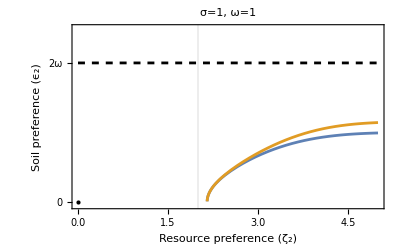

```mathematica
figS1=Plot[{(ω√(1-αc))/.par,(2 ω√((1-αc)/(3+αc)))/.par,2ω/.par},{ζ,0,5},PlotRange->{Automatic,{-0.05,2.5ω/.par}},PlotStyle->{{ColorData[97,1]},{ColorData[97,2]},{Black,Dashed}},Frame-> True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},PlotLabel->"σ=1, ω=1",LabelStyle->{FontSize->20,FontColor->Black},FrameTicks->{{{0,{2(ω/.par),"2ω"}},{{(ω/.par),"ω"},{N[2(ω/.par)/√3],"2ω/√3"}}},{Automatic,Automatic}},FrameTicksStyle->9,GridLines->{{2},{}},Epilog-> {PointSize[Large],Point[{0,0}]}]
```

Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figS1.pdf", figS1];